# Common-terminal current sharing

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

Zi+e=V1; 1ᵀi=It

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Change strand count or return geometry; inspect complex strand currents and input/loss balance.

## Derivation and interpretation

Insulated strands are connected in parallel only at the ends. The 2D Az weak form couples each conductive region to its unknown axial electric potential gradient. A controlled conducting coaxial return closes the transport problem.

Linearity yields a coupled block system for Az and the source/return voltage gradients. Impose ΣIi=20 A RMS and Ireturn=−20 A; every strand shares the source voltage gradient, while each complex Ii follows from integrating its solved current density.

Compute bundle and return Joule losses separately and compare their sum with input real power. Rac,bundle=Pbundle/|It|.b2 is valid for this pure transport case. Seven strands demonstrate the method and do not meet Q2 copper area.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"strands"->7,"diameter_m"->0.0001,"mesh_factor"->0.7,"return_factor"->2.,"outer_factor"->1.5,"minimum_segments"->24|>;parameters
```

<|strands -> 7, diameter_m -> 0.0001, mesh_factor -> 0.7, 
 
>   return_factor -> 2., outer_factor -> 1.5, minimum_segments -> 24|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"coax",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_coax_20261014005452_1e5850fa, 
 
>   source_model -> 2D_linear_triangle_Az_common_voltage_coax_FEM, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

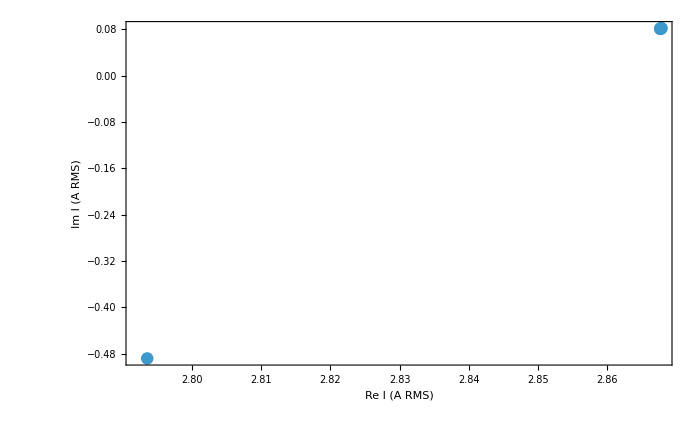

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: P01, P02; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch common-terminal